```mathematica
ClearAll["Global`*"];SetDirectory[NotebookDirectory[]];Get["./DefinitionsAndAssumptions.m"];
ClearVars;ShowVariableDefinitions
```

Definitions and assumptions for analysis of consumption and portfolio choice with risky and safe assets.

(rfree |  | log riskfree return (rate)
Rfree |  | Exp[rfree] = riskfree return (factor)
ℛtp1 |  | Realized risky return (factor)
ℛ == 𝔼_t[ℛtp1] |  | Expected risky return (factor)
𝓇tp1 == Log[ℛtp1] |  | realized log risky return (rate)
𝓇tp1 | ~ | 𝒩(𝓇 - σ^2/2,σ^2) → 𝔼_t[𝓇tp1] = 𝓇 - σ^2/2
𝓇 == Log[ℛ] |  | log expected risky return factor
𝓇 | = | Log[𝔼_t[ℛtp1]] = Log[𝔼_t[𝓇tp1]]+σ^2/2 = 𝓇-σ^2/2+σ^2/2
σ |  | standard deviation of log risky return
ϕ |  | 𝓇-rfree = log equity premium (rate)
Φ |  | Expected equity premium (factor)
ϕtp1 |  | Realized logarithmic equity premium
ϕtp1 | ~ | 𝒩(ϕ - σ^2/2,σ^2) → {𝔼_t[ϕtp1] = ϕ - σ^2/2, log 𝔼Φtp1 = ϕ - σ^2/2 + σ^2/2 = ϕ} by MathFact LogELogNorm
ϛ |  | portfolio share in the risky asset
ℜtp1 | == | Rfreetp1 + (ℛtp1-Rfreetp1)ϛ  = arithmetic (exactly correct) portfolio return
ℜ | == | 𝔼t[Rfreetp1 + (ℛtp1-Rfreetp1)ϛ] = expected arithmetic (exactly correct) portfolio return
𝔯 | == | Log[ℜ] = arithmetic (exactly correct) portfolio return)

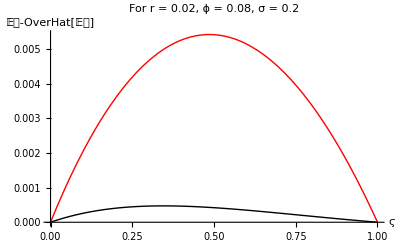

```mathematica
ClearVars;𝓇 = rfree+ϕ;Rfree=Exp[rfree];σ=0.2;rfree=0.02;ϕ=0.08;
(* First, show that the approximation of the (true) arithmetic return by the Campbell-Viceira approximation
   is good (or at least much better than the geometric approximation)*)
Needs["PlotLegends`"];
Off[NIntegrate::inumr]; (*Turn off some annoying warning messages*)
ExactMinusApproxLogExpectedPortfolioReturn = 
Plot[{𝔼𝔯[ϛ,σ]-𝔼𝔯Approx[ϛ,σ],𝔼𝔯[ϛ,σ]-𝔼𝔯Geometric[ϛ,σ]}
  ,{ϛ,0,1}
  ,AxesLabel->{"ϛ","𝔼𝔯-OverHat[𝔼𝔯]"}
  ,BaseStyle->{FontSize->14}
  ,PlotLabel->"For r = "<>ToString[rfree]<>", ϕ = "<>ToString[ϕ]<>", σ = "<>ToString[σ]
  ,PlotStyle->{Black,Red}
,PlotLegend->{"Campbell-Viceira","Geometric"}
,LegendSize->0.75
,LegendTextSpace->5
,LegendPosition->{0.,0.}
];
Export["../../Figures/ExactMinusApproxLogExpectedPortfolioReturn.pdf",ExactMinusApproxLogExpectedPortfolioReturn];
Export["../../Figures/ExactMinusApproxLogExpectedPortfolioReturn.png",ExactMinusApproxLogExpectedPortfolioReturn,ImageSize->72 9];
Export["../../Figures/ExactMinusApproxLogExpectedPortfolioReturn.svg",ExactMinusApproxLogExpectedPortfolioReturn];
Print[ExactMinusApproxLogExpectedPortfolioReturn];
On[NIntegrate::inumr];
ClearVars;
```

```mathematica
(* Calculate 𝔼t[Exp[(1-ρ) ϛ ϕtp1]; part of formula for expected utility \eqref{eq:exputil} in handout *)
𝔼tΦtp1Part = Integrate[Exp[(1-ρ)ϛ Log[Φ]] PDF[LogNormalDistribution[ϕ-σ^2/2,σ],Φ],{Φ,0,∞}]
```

ⅇ^(1/2 (-1+ρ) ϛ (-2 ϕ+σ^2 (1+(-1+ρ) ϛ)))

```mathematica
log𝔼tΦtp1Part = Simplify[Log[𝔼tΦtp1Part]]
```

1/2 (-1+ρ) ϛ (-2 ϕ+σ^2 (1+(-1+ρ) ϛ))

```mathematica
(* Simplify the expression further *)
Simpler4Sub = (1-ρ)(ϕ ϛ -ϛ(1-(1-ρ)ϛ)(σ^2/2));
Simpler5Sub = (1-ρ)(ϕ ϛ -ϛ(1-ϛ)(σ^2/2)-ρ ϛ^2(σ^2/2));
Simpler6Sub = -(ρ-1)(ϕ ϛ -ϛ(1-ϛ)(σ^2/2)-ρ ϛ^2(σ^2/2));
```

```mathematica
(* Verify that the simplification is correct *)
Simplify[log𝔼tΦtp1Part == Simpler6Sub]
```

```mathematica
(* Using this result, now compute expected utility *)
𝔼utp1 = Exp[(1-ρ)ϛ(1-ϛ)σ^2/2] Exp[log𝔼tΦtp1Part]
```

ⅇ^(1/2 (1-ρ) σ^2 (1-ϛ) ϛ+1/2 (-1+ρ) ϛ (-2 ϕ+σ^2 (1+(-1+ρ) ϛ)))

```mathematica
log𝔼utp1 = 𝔼utp1[[2]]; (* Extracts the exponent on ⅇ; for some reason, directly taking the Log does not obtain the exponent *)
```

```mathematica
(* Verify that a simpler expression (derived in the handout) is correct *)
Simplify[log𝔼utp1 == -(ρ-1) (ϕ ϛ - ϛ^2 ρ (σ^2/2))]
```

True

```mathematica
(* Calculate the approximation to the optimal portfolio share *)
Assuming[{ϛ>0,ρ>0,ϕ>0},Maximize[{ϕ ϛ - ϛ^2 ρ (σ^2/2),ϕ>0,σ>0,ρ>0},ϛ]][[2]]
```

{ϛ→Piecewise[{{ϕ/(ρ σ^2), ϕ>0&&σ>0&&ρ>0}, {Indeterminate, True}}]}

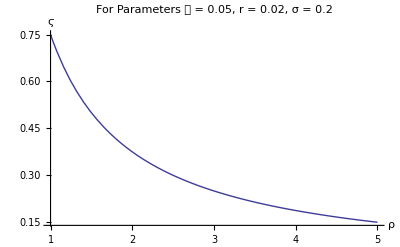

```mathematica
𝓇=0.05;rfree=0.02;ϕ=𝓇-rfree;σ=0.2;
ShareVsCRRA = Plot[ϛOptApprox[σ,ρ],{ρ,1,5}
,AxesLabel->{"ρ","ϛ"}
,PlotLabel->"For Parameters 𝓇 = "<>ToString[𝓇]<>", r = "<>ToString[rfree]<>", σ = "<>ToString[σ]
,BaseStyle->{FontSize->14}
];
Export["../../Figures/ShareVsCRRA.pdf",ShareVsCRRA];
Export["../../Figures/ShareVsCRRA.png",ShareVsCRRA,ImageSize->72 9];
Export["../../Figures/ShareVsCRRA.svg",ShareVsCRRA];
Print[ShareVsCRRA];
```

NIntegrate::inumr: The integrand Piecewise[{{1.9947114020071635` ⅇ^« 1 »/Φ, Φ > 0}, {0, True}}] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 1.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

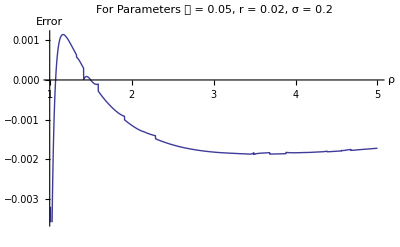

```mathematica
ShareApproxErr=Plot[{ϛOptExact[σ,ρ]-ϛOptApprox[σ,ρ]},{ρ,1.01,5}
,PlotLabel->"For Parameters 𝓇 = "<>ToString[𝓇]<>", r = "<>ToString[rfree]<>", σ = "<>ToString[σ]
,BaseStyle->{FontSize->14}
,AxesLabel->{"ρ","Error"}];
Export["../../Figures/ShareApproxErr.pdf",ShareApproxErr];
Export["../../Figures/ShareApproxErr.png",ShareApproxErr,ImageSize->72 9];
Export["../../Figures/ShareApproxErr.svg",ShareApproxErr];
Print[ShareApproxErr];
```